```mathematica
A1=1;g=-1.445;gamma=0.8;T1=0.75;height=3.2;A2=1/3;T2=3.8574932905873918*T1;nz=4096;
z0=3*height/4;
waveLen=0.4;
```

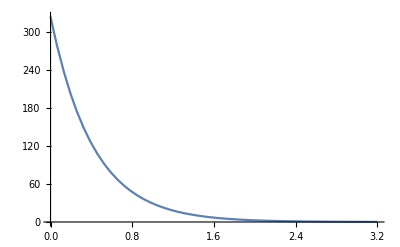

```mathematica
rho1[x_,z_]:=A1*Exp[g*(z-z0)/(gamma*T1)];
Plot[rho1[0,z],{z,0,height},PlotRange->All]
```

```mathematica
rho1[0,height/2]
```

6.86658

```mathematica
rho2[x_,z_]:=A2*Exp[g*(z-z0)/(gamma*T2)];
```

```mathematica
rho2[0,height/2]
```

0.549278

```mathematica
rho3[x_,z_]:=0.5(1+Erf[(z-z0)/yv])(rho1[x,z]-rho2[x,z])+rho2[x,z];
```

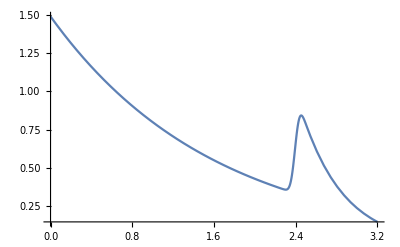

```mathematica
Plot[rho3[0,z],{z,0,height},PlotRange->All]
```

```mathematica
Press1[x_,z_]:=rho1[x,z]*gamma*T1;
```

```mathematica
Press1[0,z0]
```

0.6

```mathematica
A1*gamma*T1
```

0.6

```mathematica
Press2[x_,z_]:=rho2[x,z]*gamma*T2;
Press2new[x_,z_]:=Press2[x,z]+Press1[0,z0]-Press2[0,z0];
```

```mathematica
Press3[x_,z_]:=0.5(1+Erf[(z-z0)/yv])(Press1[x,z]-Press2new[x,z])+Press2new[x,z];
```

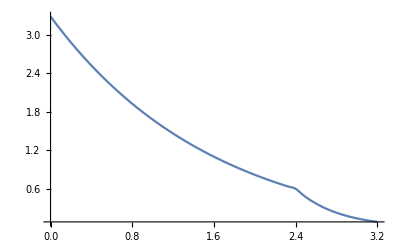

```mathematica
Plot[Press3[0,z],{z,0,height},PlotRange->All]
```

```mathematica
machpost= Sqrt[rho3[0,z0]*(-g)*waveLen/Press3[0,z0]]
atpost=(rho1[0,z0]-rho2[0,z0])/(rho1[0,z0]+rho2[0,z0])
```

0.801388

0.5

```mathematica
Press3[0,0]
rho3[0,0]
Press3[0,3.2]
rho3[0,3.2]
```

3.28053

1.49148

0.0873797

0.145633

```mathematica
rho1onlyz[z_]:=A1*Exp[g*z/(gamma*T1)];
rho1avr=NIntegrate[rho1[0,z],{z,height/2,height}]/(height/2)
```

1.74419

```mathematica
rho2avr=NIntegrate[rho2[0,z],{z,0,height/2}]/(height/2)
```

0.943221

```mathematica
atwood=(rho1avr-rho2avr)/(rho1avr+rho2avr)
```

0.298045

```mathematica
at=0.588265;mach=0.4;
yv=0.002;
rho1[x_,z_]:=(1+at)Exp[-mach^2*(1+at)*(z-z0)];
rho2[x_,z_]:=(1-at)Exp[-mach^2*(1-at)*(z-z0)];
rho3[x_,z_]:=0.5(1+Erf[(z-z0)/yv])(rho1[x,z]-rho2[x,z])+rho2[x,z];
```

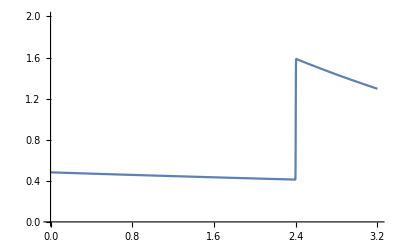

```mathematica
Plot[rho3[0,z],{z,0,height},PlotRange->{0,2}]
```

```mathematica
Press1[x_,z_]:=Exp[-mach^2*(1+at)*(z-z0)];
p1=Plot[Press1[0,z],{z,0,height}];
```

```mathematica
Press2[x_,z_]:=Exp[-mach^2*(1-at)*(z-z0)];
p2=Plot[Press2[0,z],{z,0,height}];
```

```mathematica
Press3[x_,z_]:=0.5(1+Erf[(z-z0)/yv])(Press1[x,z]-Press2[x,z])+Press2[x,z];
```

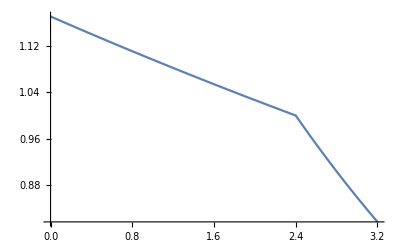

1.09662

```mathematica
Plot[Press3[0,z],{z,0,height}]
Press3[0,1]
```

```mathematica
NumberForm[0.99999999999932,16]
```

0.99999999999932

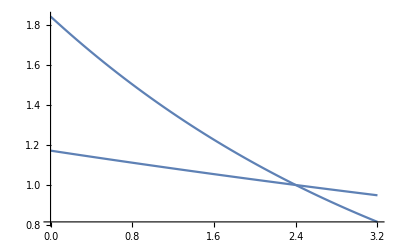

```mathematica
Show[p1,p2,PlotRange->All]
```

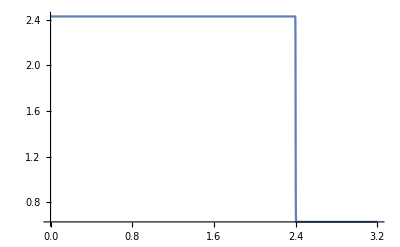

```mathematica
Plot[Press3[0,z]/rho3[0,z],{z,0,height}]
```

```mathematica
(Press3[0,0]/rho3[0,0])/(Press3[0,3.2]/rho3[0,3.2])
```

3.85749

```mathematica
z0
```

2.4

```mathematica
Plot[-D[Press3[0,z],z],{z,0,height}]
```

General::ivar: 0.0000653714 is not a valid variable.

General::ivar: 0.0653715 is not a valid variable.

General::ivar: 0.130678 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
deriverp[z_]:=D[Press3[1,z],z]
```

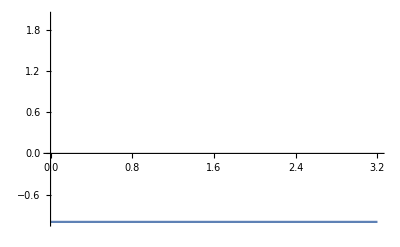

```mathematica
Plot[-%5196,{z,0,3.2},PlotRange->{-1,2}]
```

```mathematica
yv
```

0.002

```mathematica
t1
```

t1

```mathematica
T1
```

0.75

```mathematica
T2
```

2.89312

```mathematica
yv
```

0.002

```mathematica
yv=0.05
```

0.05